# Integration Rules for ∫(sin^j(z))^m(A+B sin^k(z))(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1

Domain Map

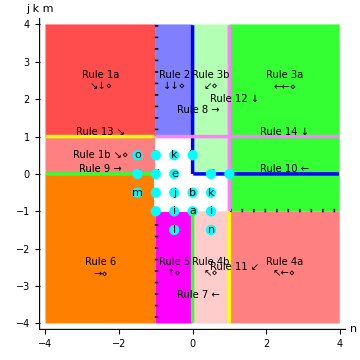

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

Integration Rules for 
∫(sin^j(z))^m(A+B sin^k(z))ⅆz when j^2=1∧k^2=1

Rule a:  ∫Sin[c+d x]^j(A+B Sin[c+d x]^-j)ⅆx

#### Derivation: Algebraic expansion

#### Rule a: If j^2=1, then

∫Sin[c+d x]^j(A+B Sin[c+d x]^-j)ⅆx  ⟶  B x+A∫Sin[c+d x]^j ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^j_.*(A_+B_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  B*x + Dist[A,Int[sin[c+d*x]^j,x]] /;
FreeQ[{c,d,A,B},x] && OneQ[j^2] && ZeroQ[j+k]
```

Rule b:  ∫(Sin[c+d x]^j)^(m/2)(A+B Sin[c+d x]^-j)ⅆx

#### Derivation: Algebraic expansion

#### Rule b1:

∫√Sin[c+d x](A+B Csc[c+d x])ⅆx  ⟶  A∫√Sin[c+d x]ⅆx +B∫1/(√Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[Sqrt[sin[c_.+d_.*x_]]*(A_+B_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  Dist[A,Int[Sqrt[sin[c+d*x]],x]] + 
  Dist[B,Int[1/Sqrt[sin[c+d*x]],x]] /;
FreeQ[{c,d,A,B},x]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (f[z]^m(1/f[z])^m)=0

#### Note: For some strange reason, Mathematica overly agressively evaluates 1/(√f[z] √(1/f[z])) to √f[z] √(1/f[z]).

#### Rule b2: If m^2=1, then

∫Csc[c+d x]^(m/2)(A+B Sin[c+d x])ⅆx  ⟶  Sin[c+d x]^(m/2)Csc[c+d x]^(m/2)∫(A+B Sin[c+d x])/Sin[c+d x]^(m/2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^(-1))^m_*(A_.+B_.*sin[c_.+d_.*x_]),x_Symbol] :=
  Dist[Sin[c+d*x]^m*Csc[c+d*x]^m,Int[(A+B*sin[c+d*x])/sin[c+d*x]^m,x]] /;
FreeQ[{c,d,A,B},x] && ZeroQ[m^2-1/4]
```

Rules 7-8:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)ⅆx

#### Derivation: Rule 5 with a=1, b=0 and n=0

#### Rule 7: If j^2=k^2=1 ∧ j k m<-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)ⅆx  ⟶  (A Cos[c+d x](Sin[c+d x]^j)^(m+j k))/(d(j k m+(k+1)/2))+
1/(j k m+(k+1)/2)∫(Sin[c+d x]^j)^(m+j k) (B(j k m+(k+1)/2)+A(j k m+(k+3)/2)Sin[c+d x]^k )ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+B_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*Sim[B*(j*k*m+(k+1)/2)+A*(j*k*m+(k+3)/2)*sin[c+d*x]^k,x],x]] /;
FreeQ[{c,d,A,B},x] && OneQ[j^2,k^2] && RationalQ[m] && j*k*m<-1
```

#### Derivation: Rule 3b with n=0

#### Rule 8: If j^2=k^2=1 ∧ j k m>0 ∧ m^2≠1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)ⅆx  ⟶  -(B Cos[c+d x](Sin[c+d x]^j)^m)/(d (j k m+(k+1)/2))+
1/(j k m+(k+1)/2)∫(Sin[c+d x]^j)^(m-j k)  (B (j k m+(k-1)/2)+A (j k m+(k+1)/2) Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+B_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  -B*Cos[c+d*x]*(Sin[c+d*x]^j)^m/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m-j*k)*(B*(j*k*m+(k-1)/2)+A*(j*k*m+(k+1)/2)*sin[c+d*x]^k),x]] /;
FreeQ[{c,d,A,B},x] && OneQ[j^2,k^2] && RationalQ[m] && j*k*m>0 && m^2≠1
```

# Integration Rules for ∫(A+B sin^k(z))(a+b sin^k(z))^n ⅆz when k^2=1

Rule c:  ∫(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)ⅆx

#### Derivation: Rule 3a with m=0 and n=1

#### Rule c: If k^2=1, then

∫(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)ⅆx  ⟶ 
((4 a A+b B(k+1))x)/4-(2b B Cos[c+d x]Sin[c+d x]^k)/(d(k+3))+(b A+a B)∫Sin[c+d x]^k ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  (4*a*A+b*B*(k+1))*x/4 - (2*b*B*Cos[c+d*x]*Sin[c+d*x]^k)/(d*(k+3)) + (b*A+a*B)*Int[sin[c+d*x]^k,x] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[k^2]
```

Rule d:  ∫(A+B Sin[c+d x]^k)/(a+b Sin[c+d x]^k)ⅆx

#### Derivation: Algebraic simplification

#### Basis: If b A-a B=0, then (A+B z)/(a+b z)=B/b

#### Rule d1: If k^2=1 ∧ b A-a B=0, then

∫(A+B Sin[c+d x]^k)/(a+b Sin[c+d x]^k)ⅆx  ⟶  (B x)/b

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]^k_.)/(a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  B*x/b /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[k^2] && ZeroQ[b*A-a*B]
```

#### Reference: G&R 2.551.2

#### Derivation: Algebraic expansion

#### Basis: (A+B z)/(a+b z)=B/b+(b A-a B)/(b(a+b z))

#### Rule d2: If a^2-b^2≠0 ∧ b A-a B≠0, then

∫(A+B Sin[c+d x])/(a+b Sin[c+d x])ⅆx  ⟶  (B x)/b+(b A-a B)/b∫1/(a+b Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_])/(a_+b_.*sin[c_.+d_.*x_]),x_Symbol] :=
  B*x/b + Dist[(b*A-a*B)/b,Int[1/(a+b*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

#### Derivation: Algebraic expansion

#### Basis: (A+B/z)/(a+b/z)=A/a-(b A-a B)/(a(b+a z))

#### Rule d3: If a^2-b^2≠0 ∧ b A-a B≠0, then

∫(A+B Csc[c+d x])/(a+b Csc[c+d x])ⅆx  ⟶  (A x)/a-(b A-a B)/a∫1/(b+a Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1))/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  A*x/a - Dist[(b*A-a*B)/a,Int[1/(b+a*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

Rule e:  ∫(A+B Sin[c+d x])/(√(a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: (A+B z)/(√(a+b z))=B/b √(a+b z)+(b A-a B)/b 1/(√(a+b z))

#### Rule e: If a^2-b^2≠0 ∧ b A-a B≠0, then

∫(A+B Sin[c+d x])/(√(a+b Sin[c+d x]))ⅆx  ⟶  B/b∫√(a+b Sin[c+d x])ⅆx+(b A-a B)/b∫1/(√(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_])/Sqrt[a_.+b_.*sin[c_.+d_.*x_]],x_Symbol] :=
  Dist[B/b,Int[Sqrt[a+b*sin[c+d*x]],x]] +
  Dist[(b*A-a*B)/b,Int[1/Sqrt[a+b*sin[c+d*x]],x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

Rule f:  ∫(A+B Csc[c+d x])(a+b Csc[c+d x])^(n/2)ⅆx

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z 1/(√f[z]√(b/f[z]))=0

#### Rule f1:

∫(A+B Csc[c+d x])/(√(b Csc[c+d x]))ⅆx  ⟶  1/(√Sin[c+d x]√(b Csc[c+d x]))∫(B+A Sin[c+d x])/(√Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]^(-1))/Sqrt[b_.*sin[c_.+d_.*x_]^(-1)],x_Symbol] :=
  Dist[1/(Sqrt[Sin[c+d*x]]*Sqrt[b*Csc[c+d*x]]),Int[(B+A*sin[c+d*x])/Sqrt[sin[c+d*x]],x]] /;
FreeQ[{b,c,d,A,B},x]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√(b+a f[z]))/(√f[z]√(a+b/f[z]))=0

#### Rule f2: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ n-1/2∈ℤ ∧ -2<n<1, then

∫(A+B Csc[c+d x])(a+b Csc[c+d x])^n ⅆx  ⟶  
(√(b+a Sin[c+d x]))/(√Sin[c+d x]√(a+b Csc[c+d x]))∫((B+A Sin[c+d x])(b+a Sin[c+d x])^n)/Sin[c+d x]^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/(Sqrt[Sin[c+d*x]]*Sqrt[a+b*Csc[c+d*x]]),
    Int[(B+A*sin[c+d*x])*(b+a*sin[c+d*x])^n/sin[c+d*x]^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && IntegerQ[n-1/2] && -2<n<1
```

∫(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Algebraic simplification

#### Basis: If b A-a B=0, then (A+B z) (a+b z)^n=B/b(a+b z)^(n+1)

#### Rule: If k^2=1 ∧ b A=a B ∧ n<0, then

∫(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  B/b∫(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_.+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[B/b,Int[(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,n},x] && OneQ[k^2] && ZeroQ[b*A-a*B] && RationalQ[n] && n<0
```

Rules 17-18:  ∫(A+B Csc[c+d x]) (a+b Csc[c+d x])^n ⅆx

#### Derivation: Rule 6 with m=0 and k=-1

#### Rule 17: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ n<-1, then

∫(A+B Csc[c+d x]) (a+b Csc[c+d x])^n ⅆx  ⟶  
(b(b A-a B) Cot[c+d x](a+b Csc[c+d x])^(n+1))/(a d (n+1) (a^2-b^2))+1/(a (n+1) (a^2-b^2)) ·
∫(A (a^2-b^2) (n+1)-a(b A-a B)(n+1)Csc[c+d x]+b(b A-a B)(n+2)Csc[c+d x]^2)(a+b Csc[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  b*(b*A-a*B)*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[Sim[A*(a^2-b^2)*(n+1)-(a*(b*A-a*B)*(n+1))*sin[c+d*x]^(-1)+
        (b*(b*A-a*B)*(n+2))*sin[c+d*x]^(-2),x]*
      (a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n<-1
```

#### Derivation: Rule 3a with m=0 and k=-1

#### Rule 18: If a^2-b^2≠0 ∧ n>1, then

∫(A+B Csc[c+d x]) (a+b Csc[c+d x])^n ⅆx  ⟶  
-(b B Cot[c+d x](a+b Csc[c+d x])^(n-1))/(d n)+1/n·
∫(a^2 A n+(b^2 B (n-1)+2 a A b n+a^2 B n)Csc[c+d x]+b(b A n+a B (2 n-1))Csc[c+d x]^2)(a+b Csc[c+d x])^(n-2)ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -b*B*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n-1)/(d*n) + 
  Dist[1/n,
    Int[Sim[a^2*A*n+(b^2*B*(n-1)+2*a*A*b*n+a^2*B*n)*sin[c+d*x]^(-1)+
        (b*(b*A*n+a*B*(2*n-1)))*sin[c+d*x]^(-2),x]*
      (a+b*sin[c+d*x]^(-1))^(n-2),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && RationalQ[n] && n>1
```

Rules 15-16:  ∫(A+B Sin[c+d x]^k) (b Sin[c+d x]^k)^n ⅆx

#### Derivation: Rule 10a inverted

#### Rule 15: If k^2=1 ∧ n<-1, then

∫(A+B Sin[c+d x]^k)(b Sin[c+d x]^k)^n ⅆx ⟶  (2 A Cos[c+d x] (b Sin[c+d x]^k)^(n+1))/(b d (2 n+k+1))+
1/(b(2 n+k+1))∫(B(2 n+k+1)+A(2n+k+3) Sin[c+d x]^k) (b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]^k_.)*(b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  2*A*Cos[c+d*x]*(b*Sin[c+d*x]^k)^(n+1)/(b*d*(2*n+k+1)) + 
  Dist[1/(b*(2*n+k+1)),
    Int[Sim[B*(2*n+k+1)+A*(2*n+k+3)*sin[c+d*x]^k,x]*(b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{b,c,d,A,B},x] && OneQ[k^2] && RationalQ[n] && n<-1
```

#### Derivation: Rule 3a or 3b with m=0 and a=0

#### Rule 16: If k^2=1 ∧ n>0, then

∫(A+B Sin[c+d x]^k) (b Sin[c+d x]^k)^n ⅆx  ⟶  -(2B Cos[c+d x](b Sin[c+d x]^k)^n)/(d (2n+k+1))+
1/(2n+k+1) ∫(b B(2n+k-1)+b A(2n+k+1)Sin[c+d x]^k)(b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_]^k_.)*(b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -2*B*Cos[c+d*x]*(b*Sin[c+d*x]^k)^n/(d*(2*n+k+1)) + 
  Dist[1/(2*n+k+1),
    Int[Sim[b*B*(2*n+k-1)+b*A*(2*n+k+1)*sin[c+d*x]^k,x]*(b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{b,c,d,A,B},x] && OneQ[k^2] && RationalQ[n] && n>0
```

# Integration Rules for ∫(sin^j(z))^m(A+B sin^k(z))(a+b sin^k(z))^n ⅆz when j^2=1∧k^2=1

Rule g:  ∫(A+B Sin[c+d x])/(Sin[c+d x](a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: (A+B z)/(z(a+b z))=A/(a z)-(b A-a B)/(a(a+b z))

#### Rule g: If a B-b A≠0, then

∫(A+B Sin[c+d x])/(Sin[c+d x](a+b Sin[c+d x]))ⅆx  ⟶  A/a∫1/Sin[c+d x]ⅆx-(b A-a B)/a∫1/(a+b Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(sin[c_.+d_.*x_]*(a_+b_.*sin[c_.+d_.*x_])),x_Symbol] :=
  Dist[A/a,Int[1/sin[c+d*x],x]] - 
  Dist[(b*A-a*B)/a,Int[1/(a+b*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[b*A-a*B]
```

Rule h:  ∫(Sin[c+d x]^(m/2)(A+B Sin[c+d x]))/(a+b Sin[c+d x])ⅆx

#### Derivation: Algebraic expansion

#### Basis: (A+B z)/(a+b z)=B/b+(b A-a B)/(b(a+b z))

#### Rule h: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m^2=1, then

∫(Sin[c+d x]^(m/2)(A+B Sin[c+d x]))/(a+b Sin[c+d x])ⅆx  ⟶ B/b ∫Sin[c+d x]^(m/2)ⅆx+(b A-a B)/b∫Sin[c+d x]^(m/2)/(a+b Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_*(A_+B_.*sin[c_.+d_.*x_])/(a_+b_.*sin[c_.+d_.*x_]),x_Symbol] :=
  Dist[B/b,Int[sin[c+d*x]^m,x]] + 
  Dist[(b*A-a*B)/b,Int[sin[c+d*x]^m/(a+b*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && ZeroQ[m^2-1/4]
```

Rule i:  ∫((A+B Sin[c+d x]) (a+b Sin[c+d x])^(n/2))/Sin[c+d x]ⅆx

#### Derivation: Algebraic expansion

#### Basis: (A+B z)/z=B+A 1/z

#### Rule i: If a^2-b^2≠0 ∧ n^2=1, then

∫((A+B Sin[c+d x]) (a+b Sin[c+d x])^(n/2))/Sin[c+d x]ⅆx  ⟶  
B∫(a+b Sin[c+d x])^(n/2)ⅆx+A∫(a+b Sin[c+d x])^(n/2)/Sin[c+d x]ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])*(a_+b_.*sin[c_.+d_.*x_])^n_/sin[c_.+d_.*x_],x_Symbol] :=
  Dist[B,Int[(a+b*sin[c+d*x])^n,x]] + 
  Dist[A,Int[(a+b*sin[c+d*x])^n/sin[c+d*x],x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && ZeroQ[n^2-1/4]
```

Rule j:  ∫(A+B Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Rule j: If a^2-b^2≠0 ∧ A-B≠0, then

∫(A+B Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx  ⟶  
B∫(1+Sin[c+d x])/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+(A-B)∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(Sqrt[sin[c_.+d_.*x_]]*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  B*Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  (A-B)*Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[A-B]
```

Rule k:  ∫((A+B Sin[c+d x])√(a+b Sin[c+d x]))/(√(e+f Sin[c+d x]))ⅆx

#### Derivation: Algebraic transformation

#### Basis: (A+B z)√(a+b z)=(a A+(b A+a B) z+b B z^2)/(√(a+b z))

#### Rule k: If a^2-b^2≠0 ∧ e^2-f^2≠0, then

∫((A+B Sin[c+d x])√(a+b Sin[c+d x]))/(√(e+f Sin[c+d x]))ⅆx  ⟶  ∫(a A+(b A+a B) Sin[c+d x]+b B Sin[c+d x]^2)/(√(a+b Sin[c+d x])√(e+f Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])*Sqrt[a_.+b_.*sin[c_.+d_.*x_]]/Sqrt[e_.+f_.*sin[c_.+d_.*x_]],x_Symbol] :=
  Int[(a*A+(b*A+a*B)*sin[c+d*x]+b*B*sin[c+d*x]^2)/(Sqrt[a+b*sin[c+d*x]]*Sqrt[e+f*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d,e,f,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[e^2-f^2]
```

Rule l:  ∫(A+B Sin[c+d x])/(Sin[c+d x]^(3/2) √(a+b Sin[c+d x]))ⅆx

#### Note: This rule is not essential, but produces simpler results.

#### Rule l1: If a^2-b^2≠0, then

∫(A-A Sin[c+d x])/(Sin[c+d x]^(3/2) √(a+b Sin[c+d x]))ⅆx  ⟶  
(2 A √(a+b Sin[c+d x]) Tan[1/2 (c-π/2+d x)])/(a d √Sin[c+d x])-(2 A)/a∫(√(a+b Sin[c+d x]))/(√Sin[c+d x] (1+Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(sin[c_.+d_.*x_]^(3/2)*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  2*A*Sqrt[a+b*Sin[c+d*x]]*Tan[(c-Pi/2+d*x)/2]/(a*d*Sqrt[Sin[c+d*x]]) - 
  2*A/a*Int[Sqrt[a+b*sin[c+d*x]]/(Sqrt[sin[c+d*x]]*(1+sin[c+d*x])),x] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && ZeroQ[A+B]
```

#### Derivation: Algebraic expansion

#### Note: This rule is not essential, but produces simpler results.

#### Rule l2: If a^2-b^2≠0 ∧ A+B≠0, then

∫(A+B Sin[c+d x])/(Sin[c+d x]^(3/2) √(a+b Sin[c+d x]))ⅆx  ⟶  
(A+B)∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+A∫(1-Sin[c+d x])/(Sin[c+d x]^(3/2) √(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(sin[c_.+d_.*x_]^(3/2)*Sqrt[a_+b_.*sin[c_.+d_.*x_]]),x_Symbol] :=
  Dist[A+B,Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] + 
  Dist[A,Int[(1-sin[c+d*x])/(sin[c+d*x]^(3/2)*Sqrt[a+b*sin[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[A+B]
```

Rule m:  ∫(A+B Sin[c+d x])/(√Sin[c+d x] (a+b Sin[c+d x])^(3/2))ⅆx

#### Note: This rule is not essential, but produces simpler results.

#### Rule m1: If a^2-b^2≠0, then

∫(A+A Sin[c+d x])/(√Sin[c+d x] (a+b Sin[c+d x])^(3/2)) ⅆx  ⟶  
(2A(a-b) √Sin[c+d x] Tan[1/2 (c-π/2+d x)])/(a d(a+b) √(a+b Sin[c+d x]))+(2 A)/(a(a+b))∫(√(a+b Sin[c+d x]))/(√Sin[c+d x] (1+Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(Sqrt[sin[c_.+d_.*x_]]*(a_+b_.*sin[c_.+d_.*x_])^(3/2)),x_Symbol] :=
  2*A*(a-b)*Sqrt[Sin[c+d*x]]*Tan[(c-Pi/2+d*x)/2]/(a*d*(a+b)*Sqrt[a+b*Sin[c+d*x]]) + 
  Dist[2*A/(a*(a+b)),Int[Sqrt[a+b*sin[c+d*x]]/(Sqrt[sin[c+d*x]]*(1+sin[c+d*x])),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && ZeroQ[A-B]
```

#### Derivation: Algebraic expansion

#### Note: This rule is not essential, but produces simpler results.

#### Rule m2: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ A-B≠0, then

∫(A+B Sin[c+d x])/(√Sin[c+d x] (a+b Sin[c+d x])^(3/2)) ⅆx  ⟶  
(A-B)/(a-b)∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx-(b A-a B)/(a-b)∫(1+Sin[c+d x])/(√Sin[c+d x] (a+b Sin[c+d x])^(3/2))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])/(Sqrt[sin[c_.+d_.*x_]]*(a_+b_.*sin[c_.+d_.*x_])^(3/2)),x_Symbol] :=
  Dist[(A-B)/(a-b),Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x]] - 
  Dist[(b*A-a*B)/(a-b),Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*(a+b*sin[c+d*x])^(3/2)),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && NonzeroQ[A-B]
```

Rule n:  ∫((A+B Sin[c+d x])√(a+b Sin[c+d x]))/Sin[c+d x]^(3/2)ⅆx

#### Derivation: Algebraic expansion

#### Note: This rule is not essential, but produces simpler results.

#### Rule n: If a^2-b^2≠0, then

∫((A+B Sin[c+d x])√(a+b Sin[c+d x]))/Sin[c+d x]^(3/2)ⅆx  ⟶  
(b (A-B)+a (A+B))∫1/(√Sin[c+d x] √(a+b Sin[c+d x]))ⅆx+∫(a A-(a A-b B) Sin[c+d x]+b B Sin[c+d x]^2)/(Sin[c+d x]^(3/2) √(a+b Sin[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*sin[c_.+d_.*x_])*Sqrt[a_+b_.*sin[c_.+d_.*x_]]/sin[c_.+d_.*x_]^(3/2),x_Symbol] :=
  (b*(A-B)+a*(A+B))*Int[1/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Int[Sim[a*A-(a*A-b*B)*sin[c+d*x]+b*B*sin[c+d*x]^2,x]/(sin[c+d*x]^(3/2)*Sqrt[a+b*sin[c+d*x]]),x] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2]
```

Rule o:  ∫(√Sin[c+d x] (A+B Sin[c+d x]))/(a+b Sin[c+d x])^(3/2)ⅆx

#### Derivation: Algebraic expansion

#### Note: This rule is not essential, but produces simpler results.

#### Rule o: If a^2-b^2≠0 ∧ b A-a B≠0, then

∫(√Sin[c+d x] (A+B Sin[c+d x]))/(a+b Sin[c+d x])^(3/2)ⅆx  ⟶  
B/b∫(1+Sin[c+d x])/(√Sin[c+d x]√(a+b Sin[c+d x]))ⅆx+1/b∫(-a B+(A b-(a+b) B) Sin[c+d x])/(√Sin[c+d x](a+b Sin[c+d x])^(3/2))ⅆx

#### Program code:

```mathematica
Int[Sqrt[sin[c_.+d_.*x_]]*(A_+B_.*sin[c_.+d_.*x_])/(a_+b_.*sin[c_.+d_.*x_])^(3/2),x_Symbol] :=
  B/b*Int[(1+sin[c+d*x])/(Sqrt[sin[c+d*x]]*Sqrt[a+b*sin[c+d*x]]),x] + 
  Dist[1/b,Int[Sim[-a*B+(A*b-(a+b)*B)*sin[c+d*x],x]/(Sqrt[sin[c+d*x]]*(a+b*sin[c+d*x])^(3/2)),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

Rule p:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)(b Sin[c+d x]^k)^n ⅆx

#### Derivation: Algebraic simplification

#### Rule p1: If k^2=1 ∧ m∈ℤ, then

∫Sin[c+d x]^m(A+B Sin[c+d x]^k)(b Sin[c+d x]^k)^n ⅆx  ⟶  
1/b^(k m)∫(A+B Sin[c+d x]^k)(b Sin[c+d x]^k)^(k m+n)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_.*(A_+B_.*sin[c_.+d_.*x_]^k_.)*(b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[1/b^(k*m),Int[(A+B*sin[c+d*x]^k)*(b*sin[c+d*x]^k)^(k*m+n),x]] /;
FreeQ[{b,c,d,A,B,n},x] && OneQ[k^2] && IntegerQ[m]
```

#### Derivation: Piecewise constant extraction

#### Basis: If j^2=1, then ∂_z (√(b f[z]^k))/((√(f[z]^j))^(j k))=0

#### Rule p2: If j^2=k^2=1 ∧ m-1/2∈ℤ ∧ n-1/2∈ℤ ∧ n>0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)(b Sin[c+d x]^k)^n ⅆx  ⟶  
(b^(n-1/2)√(b Sin[c+d x]^k))/((√(Sin[c+d x]^j))^(j k))∫Sin[c+d x]^(j m+k n)(A+B Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+B_.*sin[c_.+d_.*x_]^k_.)*(b_*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[b^(n-1/2)*Sqrt[b*Sin[c+d*x]^k]/(Sqrt[Sin[c+d*x]^j])^(j*k),
    Int[sin[c+d*x]^(j*m+k*n)*(A+B*sin[c+d*x]^k),x]] /;
FreeQ[{b,c,d,A,B},x] && OneQ[j^2,k^2] && IntegerQ[m-1/2] && IntegerQ[n-1/2] && n>0
```

#### Derivation: Piecewise constant extraction

#### Basis: If j^2=1, then ∂_z ((√(f[z]^j))^(j k))/(√(b f[z]^k))=0

#### Rule p3: If j^2=k^2=1 ∧ m-1/2∈ℤ ∧ n-1/2∈ℤ ∧ n<0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k)(b Sin[c+d x]^k)^n ⅆx  ⟶  
(b^(n+1/2)(√(Sin[c+d x]^j))^(j k))/(√(b Sin[c+d x]^k))∫Sin[c+d x]^(j m+k n)(A+B Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_+B_.*sin[c_.+d_.*x_]^k_.)*(b_*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[b^(n+1/2)*(Sqrt[Sin[c+d*x]^j])^(j*k)/Sqrt[b*Sin[c+d*x]^k],
    Int[sin[c+d*x]^(j*m+k*n)*(A+B*sin[c+d*x]^k),x]] /;
FreeQ[{b,c,d,A,B},x] && OneQ[j^2,k^2] && IntegerQ[m-1/2] && IntegerQ[n-1/2] && n<0
```

Rule q:  ∫(Sin[c+d x]^j)^m(A+B Csc[c+d x])(a+b Csc[c+d x])^n ⅆx

#### Derivation: Algebraic simplification

#### Rule q1: If j^2=1 ∧ a^2-b^2≠0 ∧ -1<m≤1, then

∫((Sin[c+d x]^j)^m(A+B Csc[c+d x]))/(a+b Csc[c+d x])ⅆx  ⟶  ∫((Sin[c+d x]^j)^m(B+A Sin[c+d x]))/(b+a Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^(-1))/(a_+b_.*sin[c_.+d_.*x_]^(-1)),x_Symbol] :=
  Int[(sin[c+d*x]^j)^m*(B+A*sin[c+d*x])/(b+a*sin[c+d*x]),x] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2] && NonzeroQ[a^2-b^2] && RationalQ[m] && -1<m≤1
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√(b+a f[z]))/(√f[z]√(a+b/f[z]))=0

#### Rule q2: If a^2-b^2≠0 ∧ m∈ℤ ∧ n-1/2∈ℤ ∧ ((m=1 ∧ -1<n<1) ∨ (m=-1 ∧ -2<n<0)), then

∫Sin[c+d x]^m(A+B Csc[c+d x])(a+b Csc[c+d x])^n ⅆx  ⟶  
(√(b+a Sin[c+d x]))/(√Sin[c+d x]√(a+b Csc[c+d x]))∫Sin[c+d x]^(m-n-1)(B+A Sin[c+d x]) (b+a Sin[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]^m_.*(A_.+B_.*sin[c_.+d_.*x_]^(-1))*(a_.+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/(Sqrt[Sin[c+d*x]]*Sqrt[a+b*Csc[c+d*x]]),
    Int[sin[c+d*x]^(m-n-1)*(B+A*sin[c+d*x])*(b+a*sin[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && IntegerQ[m] && IntegerQ[n-1/2] &&
  (m==1 && -1<n<1 || m==-1 && -2<n<0)
```

#### Derivation: Piecewise constant extraction

#### Basis: If j^2=1, then ∂_z (√(b+a f[z]))/((√(f[z]^j))^j √(a+b f[z]^-1))=0

#### Rule q3: If j^2=1 ∧ a^2-b^2≠0 ∧ m-1/2∈ℤ ∧ n-1/2∈ℤ ∧ 0≤j m-n≤1, then

∫(Sin[c+d x]^j)^m(A+B Csc[c+d x])(a+b Csc[c+d x])^n ⅆx  ⟶  
(√(b+a Sin[c+d x]))/((√(Sin[c+d x]^j))^j √(a+b Csc[c+d x]))∫Sin[c+d x]^(j m-n-1)(B+A Sin[c+d x])(b+a Sin[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^(-1))*(a_.+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  Dist[Sqrt[b+a*Sin[c+d*x]]/((Sqrt[Sin[c+d*x]^j])^j*Sqrt[a+b*Csc[c+d*x]]),
    Int[sin[c+d*x]^(j*m-n-1)*(B+A*sin[c+d*x])*(b+a*sin[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2] && NonzeroQ[a^2-b^2] && 
  IntegerQ[m-1/2] && IntegerQ[n-1/2] && -1<n<1 && 0≤j*m-n≤1
```

Rule r:  ∫Csc[c+d x]^m (A+B Sin[c+d x])(a+b Sin[c+d x])^n ⅆx

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√f[z]√(1/f[z]))=0

#### Rule r: If m-1/2∈ℤ ∧ -1<m<2 ∧ -2<n<1, then

∫Csc[c+d x]^m (A+B Sin[c+d x])(a+b Sin[c+d x])^n ⅆx  ⟶  
√Csc[c+d x]√Sin[c+d x]∫((A+B Sin[c+d x])(a+b Sin[c+d x])^n)/Sin[c+d x]^m ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^(-1))^m_*(A_.+B_.*sin[c_.+d_.*x_])*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  Dist[Sqrt[Csc[c+d*x]]*Sqrt[Sin[c+d*x]],
    Int[(A+B*sin[c+d*x])*(a+b*sin[c+d*x])^n/sin[c+d*x]^m,x]] /;
FreeQ[{a,b,c,d,A,B},x] && IntegerQ[m-1/2] && RationalQ[n] && -1<m<2 && -2<n<1
```

Rules 13-14:  ∫Sin[c+d x](A+B Sin[c+d x])(a+b Sin[c+d x])^n ⅆx

#### Derivation: Rule 1a with j m=1 and k=1

#### Rule 13: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ n<-1, then

∫Sin[c+d x](A+B Sin[c+d x]) (a+b Sin[c+d x])^n ⅆx  ⟶  
(a (b A-a B) Cos[c+d x](a+b Sin[c+d x])^(n+1))/(b d(n+1)(a^2-b^2))-1/(b(n+1) (a^2-b^2))·
∫(b (n+1)(b A-a B)+(a^2 B-a b A(n+2)+b^2 B(n+1)) Sin[c+d x]) (a+b Sin[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]*(A_+B_.*sin[c_.+d_.*x_])*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  a*(b*A-a*B)*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) - 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Sim[b*(n+1)*(b*A-a*B)+(a^2*B-a*b*A*(n+2)+b^2*B*(n+1))*sin[c+d*x],x]*
      (a+b*sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n<-1
```

#### Derivation: Rule 14b with n=-1

#### Note: This is an unnecessary special case of rule 14b, but it saves a trivial step.

#### Rule 14a: If b A-a B≠0, then

∫(Sin[c+d x] (A+B Sin[c+d x]))/(a+b Sin[c+d x])ⅆx  ⟶  -(B Cos[c+d x])/(b d)+(b A-a B)/b∫Sin[c+d x]/(a+b Sin[c+d x])ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]*(A_+B_.*sin[c_.+d_.*x_])/(a_+b_.*sin[c_.+d_.*x_]),x_Symbol] :=
  -B*Cos[c+d*x]/(b*d) + 
  Dist[(b*A-a*B)/b,Int[sin[c+d*x]/(a+b*sin[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[b*A-a*B]
```

#### Derivation: Rule 2 with j m=1 and k=1

#### Rule 14b: If n>-1 ∧ n≠1, then

∫Sin[c+d x](A+B Sin[c+d x]) (a+b Sin[c+d x])^n ⅆx  ⟶  
-(B Cos[c+d x](a+b Sin[c+d x])^(n+1))/(b d (n+2))+
1/(b (n+2))∫(b B (n+1)-(a B-b A(n+2)) Sin[c+d x])(a+b Sin[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[sin[c_.+d_.*x_]*(A_+B_.*sin[c_.+d_.*x_])*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  -B*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n+1)/(b*d*(n+2)) + 
  Dist[1/(b*(n+2)),Int[Sim[b*B*(n+1)-(a*B-b*A*(n+2))*sin[c+d*x],x]*(a+b*sin[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && RationalQ[n] && n>-1 && n≠1
```

Rules 11-12:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)ⅆx   j k m<-1???

#### Derivation: Rule 4a with n=1

#### Rule 11: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ b A-a B≠0 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 , then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)ⅆx  ⟶  
(a A Cos[c+d x] (Sin[c+d x]^j)^(m+j k))/(d(j k m+(k+1)/2))+1/(j k m+(k+1)/2)·
∫(Sin[c+d x]^j)^(m+j k) ((b A+a B) (j k m+(k+1)/2)+(a A (j k m+(k+3)/2)+b B (j k m+(k+1)/2)) Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  a*A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[(b*A+a*B)*(j*k*m+(k+1)/2)+(a*A*(j*k*m+(k+3)/2)+b*B*(j*k*m+(k+1)/2))*sin[c+d*x]^k,x],x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && 
  RationalQ[m] && j*k*m+(k+1)/2≠0 && j*k*m≤-1
```

#### Derivation: Rule 3a with n=1

#### Rule 12: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ b A-a B≠0 ∧ j k m≥-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)ⅆx  ⟶  
-(b B Cos[c+d x](Sin[c+d x]^j)^(m+j k))/(d (j k m+(k+3)/2))+1/(j k m+(k+3)/2)·
∫(Sin[c+d x]^j)^m (a A (j k m+(k+3)/2)+b B (j k m+(k+1)/2)+(b A+a B) (j k m+(k+3)/2) Sin[c+d x]^k)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.),x_Symbol] :=
  -b*B*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)/(d*(j*k*m+(k+3)/2)) + 
  Dist[1/(j*k*m+(k+3)/2),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*A*(j*k*m+(k+3)/2)+b*B*(j*k*m+(k+1)/2)+(b*A+a*B)*(j*k*m+(k+3)/2)*sin[c+d*x]^k,x],x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && 
  RationalQ[m] && j*k*m≥-1
```

Rules 9-10:  ∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k)(a+b Sin[c+d x]^k)^n ⅆx

#### Reference: G&R 2.551.1

#### Derivation: Rule 1b with j m=(k-1)/2

#### Rule 9: If k^2=1 ∧ a^2-b^2≠0 ∧ b A-a B≠0 ∧ n<-1, then

∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-((b A-a B) Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^(n+1))/(d (n+1) (a^2-b^2))+
1/((n+1) (a^2-b^2))∫Sin[c+d x]^((k-1)/2)((a A-b B)(n+1)-(b A-a B)(n+2)Sin[c+d x]^k) (a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_])*(a_+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  -(b*A-a*B)*Cos[c+d*x]*(a+b*Sin[c+d*x])^(n+1)/(d*(n+1)*(a^2-b^2)) +
  Dist[1/((n+1)*(a^2-b^2)),
    Int[Sim[(a*A-b*B)*(n+1)-(b*A-a*B)*(n+2)*sin[c+d*x],x]*(a+b*sin[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n<-1
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(A_.+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -(b*A-a*B)*Cot[c+d*x]*(a+b*Csc[c+d*x])^(n+1)/(d*(n+1)*(a^2-b^2)) + 
  Dist[1/((n+1)*(a^2-b^2)),
    Int[sin[c+d*x]^(-1)*
      Sim[(a*A-b*B)*(n+1)-(b*A-a*B)*(n+2)*sin[c+d*x]^(-1),x]*(a+b*sin[c+d*x]^(-1))^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n<-1
```

#### Reference: G&R 2.551.1 inverted

#### Derivation: Rule 3b with j m=(k-1)/2

#### Rule 10: If k^2=1 ∧ a^2-b^2≠0 ∧ n>0 ∧ n≠1, then

∫Sin[c+d x]^((k-1)/2)(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(B Cos[c+d x]Sin[c+d x]^((k-1)/2)(a+b Sin[c+d x]^k)^n)/(d (n+1))+
1/(n+1)∫Sin[c+d x]^((k-1)/2)(b B n+a A (n+1)+(a B n+b A (n+1)) Sin[c+d x]^k) (a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*sin[c_.+d_.*x_])*(a_.+b_.*sin[c_.+d_.*x_])^n_,x_Symbol] :=
  -B*Cos[c+d*x]*(a+b*Sin[c+d*x])^n/(d*(n+1)) + 
  Dist[1/(n+1),
    Int[Sim[b*B*n+a*A*(n+1)+(a*B*n+b*A*(n+1))*sin[c+d*x],x]*(a+b*sin[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && RationalQ[n] && n>0 && n≠1
```

```mathematica
Int[sin[c_.+d_.*x_]^(-1)*(A_.+B_.*sin[c_.+d_.*x_]^(-1))*(a_+b_.*sin[c_.+d_.*x_]^(-1))^n_,x_Symbol] :=
  -B*Cot[c+d*x]*(a+b*Csc[c+d*x])^n/(d*(n+1)) + 
  Dist[1/(n+1),
    Int[sin[c+d*x]^(-1)*
      Sim[b*B*n+a*A*(n+1)+(a*B*n+b*A*(n+1))*sin[c+d*x]^(-1),x]*(a+b*sin[c+d*x]^(-1))^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && RationalQ[n] && n>0 && n≠1
```

Rules 1-6:  ∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx

#### Derivation: Rule 1a, 1b or 6 with b A-a B=0

#### Derivation: Algebraic simplification

#### Basis: If b A-a B=0, then A+B z=B/b(a+b z)

#### Rule: If j^2=k^2=1 ∧ b A-a B=0 ∧ n≤-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
B/b∫(Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  Dist[B/b,Int[(sin[c+d*x]^j)^m*(a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,m},x] && OneQ[j^2,k^2] && ZeroQ[b*A-a*B] && RationalQ[n] && n<0
```

#### Derivation: Recurrence 1 with A=0, B=A, C=B and m=m-1

#### Rule 1a: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ b A-a B≠0 ∧ j k m>1 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a(b A-a B) Cos[c+d x] (Sin[c+d x]^j)^(m-j k) (a+b Sin[c+d x]^k)^(n+1))/(b d (n+1) (a^2-b^2))-
1/(b(n+1)(a^2-b^2))∫(Sin[c+d x]^j)^(m-2j k)·
(a(b A-a B)(j k m+(k-3)/2)+b(b A-a B)(n+1)Sin[c+d x]^k-(b(a A-b B)(n+1)+a(b A-a B)(j k m+(k-1)/2))Sin[c+d x]^(2k))·
(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*(b*A-a*B)*Cos[c+d*x]*(Sin[c+d*x]^j)^(m-j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(n+1)*(a^2-b^2)) - 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^(m-2*j*k)*
      Sim[a*(b*A-a*B)*(j*k*m+(k-3)/2)+b*(b*A-a*B)*(n+1)*sin[c+d*x]^k-
        (b*(a*A-b*B)*(n+1)+a*(b*A-a*B)*(j*k*m+(k-1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && j*k*m>1 && n<-1
```

#### Derivation: Recurrence 1 with C=0

#### Derivation: Recurrence 6 with A=0, B=A, C=B and m=m-1

#### Rule 1b: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ b A-a B≠0 ∧ 0<j k m<1 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-((b A-a B) Cos[c+d x] (Sin[c+d x]^j)^m (a+b Sin[c+d x]^k)^(n+1))/(d (n+1) (a^2-b^2))+
1/((n+1)(a^2-b^2))∫(Sin[c+d x]^j)^(m-j k)·
((b A-a B)(j k m+(k-1)/2)+(a A-b B)(n+1)Sin[c+d x]^k-(b A-a B)(j k m+n+(k+3)/2)Sin[c+d x]^(2k))·
(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -(b*A-a*B)*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^(n+1)/(d*(n+1)*(a^2-b^2)) + 
  Dist[1/((n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[(b*A-a*B)*(j*k*m+(k-1)/2)+(a*A-b*B)*(n+1)*sin[c+d*x]^k-
        (b*A-a*B)*(j*k*m+n+(k+3)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && 0<j*k*m<1 && n<-1
```

#### Derivation: Recurrence 2 with A=0, B=A, C=B and m=m-1

#### Rule 2: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m>1 ∧ -1≤n<0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(B Cos[c+d x](Sin[c+d x]^j)^(m-j k)(a+b Sin[c+d x]^k)^(n+1))/(b d (j k m+n+(k+1)/2))+
1/(b (j k m+n+(k+1)/2))∫(Sin[c+d x]^j)^(m-2j k)·
(a B (j k m+(k-3)/2)+b B(j k m+n+(k-1)/2)Sin[c+d x]^k+(b A(n+1)+(b A-a B)(j k m+(k-1)/2))Sin[c+d x]^(2k))·
(a+b Sin[c+d x]^k)^nⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  -B*Cos[c+d*x]*(Sin[c+d*x]^j)^(m-j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(b*d*(j*k*m+n+(k+1)/2)) + 
  Dist[1/(b*(j*k*m+n+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m-2*j*k)*
      Sim[a*B*(j*k*m+(k-3)/2)+b*B*(j*k*m+n+(k-1)/2)*sin[c+d*x]^k+
        (b*A*(n+1)+(b*A-a*B)*(j*k*m+(k-1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m>1 && -1≤n<0
```

#### Derivation: Recurrence 3 with A=a A, B=b A+a B, C=b B and n=n-1

#### Rule 3a: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m≥-1 ∧ j k m≠1 ∧ n>1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(b B Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n-1))/(d (j k m+n+(k+1)/2))+
1/(j k m+n+(k+1)/2) ∫(Sin[c+d x]^j)^m·
(a (a A n+(a A+b B)(j k m+(k+1)/2))+(a (2b A+a B)+(a^2 B+2 a b A+b^2 B)(j k m+n+(k-1)/2))Sin[c+d x]^k+b(a B (n-1)+(b A+a B) (j k m+n+(k+1)/2))Sin[c+d x]^(2k))·
(a+b Sin[c+d x]^k)^(n-2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  -b*B*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-1)/(d*(j*k*m+n+(k+1)/2)) + 
  Dist[1/(j*k*m+n+(k+1)/2),
    Int[(sin[c+d*x]^j)^m*
      Sim[a*(a*A*n+(a*A+b*B)*(j*k*m+(k+1)/2))+
        (a*(2*b*A+a*B)+(a^2*B+2*a*b*A+b^2*B)*(j*k*m+n+(k-1)/2))*sin[c+d*x]^k+
        b*(a*B*(n-1)+(b*A+a*B)*(j*k*m+n+(k+1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-2),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m≥-1 && j*k*m≠1 && n>1
```

#### Derivation: Recurrence 2 with A=a A, B=b A+a B, C=b B and n=n-1

#### Derivation: Recurrence 3 with A=0, B=A, C=B and m=m-1

#### Rule 3b: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m>0 ∧ j k m≠1 ∧ 0<n<1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
-(B Cos[c+d x](Sin[c+d x]^j)^m(a+b Sin[c+d x]^k)^n)/(d (j k m+n+(k+1)/2))+
1/(j k m+n+(k+1)/2) ∫(Sin[c+d x]^j)^(m-j k)·
(a B(j k m+(k-1)/2)+(a A+(a A+b B)(j k m+n+(k-1)/2))Sin[c+d x]^k+(n(b A+a B)+b A(j k m+(k+1)/2))Sin[c+d x]^(2k))·
(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  -B*Cos[c+d*x]*(Sin[c+d*x]^j)^m*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+n+(k+1)/2)) + 
  Dist[1/(j*k*m+n+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m-j*k)*
      Sim[a*B*(j*k*m+(k-1)/2)+(a*A+(a*A+b*B)*(j*k*m+n+(k-1)/2))*sin[c+d*x]^k+
        (n*(b*A+a*B)+b*A*(j*k*m+(k+1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m>0 && j*k*m≠1 && 0<n<1
```

#### Derivation: Recurrence 4 with A=a A, B=b A+a B, C=b B and n=n-1

#### Rule 4a: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m<-1 ∧ n>1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(a A Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^(n-1))/(d(j k m+(k+1)/2))+
1/(j k m+(k+1)/2)∫(Sin[c+d x]^j)^(m+j k)·
(a ((b A+a B)(j k m+(k+1)/2)-b A (n-1))+(a^2 A+(a^2 A+2 a b B+b^2 A) (j k m+(k+1)/2)) Sin[c+d x]^k+b(a A n+(a A+b B)(j k m+(k+1)/2))Sin[c+d x]^(2k))·
(a+b Sin[c+d x]^k)^(n-2)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  a*A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n-1)/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[a*((b*A+a*B)*(j*k*m+(k+1)/2)-b*A*(n-1))+
        (a^2*A+(a^2*A+2*a*b*B+b^2*A)*(j*k*m+(k+1)/2))*sin[c+d*x]^k+
        b*(a*A*n+(a*A+b*B)*(j*k*m+(k+1)/2))*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-2),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m<-1 && n>1
```

#### Derivation: Recurrence 4 with C=0

#### Rule 4b: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m<-1 ∧ 0<n≤1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(A Cos[c+d x] (Sin[c+d x]^j)^(m+j k) (a+b Sin[c+d x]^k)^n)/(d(j k m+(k+1)/2))+
1/(j k m+(k+1)/2)∫(Sin[c+d x]^j)^(m+j k)·
(a B(j k m+(k+1)/2)-b A n+(a A+(a A+b B) (j k m+(k+1)/2)) Sin[c+d x]^k+b A(j k m+n+(k+3)/2)Sin[c+d x]^(2k))·
(a+b Sin[c+d x]^k)^(n-1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_.,x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^n/(d*(j*k*m+(k+1)/2)) + 
  Dist[1/(j*k*m+(k+1)/2),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[a*B*(j*k*m+(k+1)/2)-b*A*n+(a*A+(a*A+b*B)*(j*k*m+(k+1)/2))*sin[c+d*x]^k+
        b*A*(j*k*m+n+(k+3)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m<-1 && 0<n≤1
```

#### Derivation: Recurrence 5 with C=0

#### Rule 5: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ j k m+(k+1)/2≠0 ∧ j k m≤-1 ∧ -1≤n<0, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(A Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n+1))/(a d(j k m+(k+1)/2))+
1/(a (j k m+(k+1)/2))∫(Sin[c+d x]^j)^(m+j k)·
((a B-b A)(j k m+(k+1)/2)-b A (n+1)+a A(j k m+(k+3)/2)Sin[c+d x]^k+b A(j k m+n+(k+3)/2)Sin[c+d x]^(2k) )·
(a+b Sin[c+d x]^k)^nⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  A*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(a*d*(j*k*m+(k+1)/2)) + 
  Dist[1/(a*(j*k*m+(k+1)/2)),
    Int[(sin[c+d*x]^j)^(m+j*k)*
      Sim[(a*B-b*A)*(j*k*m+(k+1)/2)-b*A*(n+1)+a*A*(j*k*m+(k+3)/2)*sin[c+d*x]^k+
        b*A*(j*k*m+n+(k+1)/2+2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && RationalQ[m,n] && 
  j*k*m+(k+1)/2≠0 && j*k*m≤-1 && -1≤n<0
```

#### Derivation: Recurrence 6 with C=0

#### Rule 6: If j^2=k^2=1 ∧ a^2-b^2≠0 ∧ b A-a B≠0 ∧ j k m<0 ∧ n<-1, then

∫(Sin[c+d x]^j)^m(A+B Sin[c+d x]^k) (a+b Sin[c+d x]^k)^n ⅆx  ⟶  
(b(b A-a B) Cos[c+d x](Sin[c+d x]^j)^(m+j k)(a+b Sin[c+d x]^k)^(n+1))/(a d (n+1) (a^2-b^2))+
1/(a (n+1) (a^2-b^2)) ∫(Sin[c+d x]^j)^m·
(A (a^2-b^2) (n+1)-b(b A-a B)(j k m+(k+1)/2)-a(b A-a B)(n+1)Sin[c+d x]^k+b(b A-a B)(j k m+n+(k+5)/2)Sin[c+d x]^(2k))·
(a+b Sin[c+d x]^k)^(n+1)ⅆx

#### Program code:

```mathematica
Int[(sin[c_.+d_.*x_]^j_.)^m_.*(A_.+B_.*sin[c_.+d_.*x_]^k_.)*(a_+b_.*sin[c_.+d_.*x_]^k_.)^n_,x_Symbol] :=
  b*(b*A-a*B)*Cos[c+d*x]*(Sin[c+d*x]^j)^(m+j*k)*(a+b*Sin[c+d*x]^k)^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[(sin[c+d*x]^j)^m*
      Sim[A*(a^2-b^2)*(n+1)-b*(b*A-a*B)*(j*k*m+(k+1)/2)-a*(b*A-a*B)*(n+1)*sin[c+d*x]^k+
        b*(b*A-a*B)*(j*k*m+n+(k+5)/2)*sin[c+d*x]^(2*k),x]*
      (a+b*sin[c+d*x]^k)^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && OneQ[j^2,k^2] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && 
  RationalQ[m,n] && j*k*m<0 && n<-1
```